# Neural Logic

```mathematica
Get["neural-logic.m",Path->NotebookDirectory[]];
```

```mathematica
?neurallogic`*
```

## Learn XOR

## Generate training data

```mathematica
numBooleanVariables=10;
Echo[2^numBooleanVariables];
bf=BooleanConvert[Xor[#1,#2,#3,#4,#5,#6,#7,#8,#9,#10]&,"BooleanFunction"];
maxExamples=200;
examples=Map[With[{x=RandomChoice[{0,1},numBooleanVariables]},Soften/@x->{Soften[Boole[bf@@x]]}]&,Range[maxExamples]];
{trainData,testData}=[examples,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
```

1024

## Create BNN

```mathematica
{softNet,hardNet}=BinaryNN[{NeuralDNFLayer[numBooleanVariables,50,50],NeuralDNFLayer[50,50,50],NeuralDNFLayer[50,50,1]}];
```

```mathematica
bnn=AppendLoss[softNet]
```

NetGraph[<>]

## Train BNN

```mathematica
{trainedBNN,resultsObject}=NetTrain[softNet,trainData,{"TrainedNet","ResultsObject"},
ValidationSet->testData,
(*LossFunction->"Loss",
BatchSize->16,*)
Method->{"ADAM"},
MaxTrainingRounds->10000];
```

## Evaluate

```mathematica
resultsObject["RoundMeasurements"]
trainedNet=NetExtract[trainedBNN,"NeuralLogicNet"];
```

<|Loss→4.12926×10^-9|>

```mathematica
Log[1]
```

0

### Evaluate soft net

```mathematica
randomTestSample=RandomSample[testData,UpTo[10000]];
softPredictionTargetPairs=[{trainedNet[First[#]],First[Last[#]]}&,randomTestSample];
softPredictionTargetPairs={Harden[#[[1]]],#[[2]]}&/@softPredictionTargetPairs;
Sort[Counts[softPredictionTargetPairs]]
```

<|{{False},0.}→100|>

### Evaluate hard net

```mathematica
trainedBinaryNN=HardBinaryNN[hardNet,trainedNet];
```

```mathematica
hardPredictionTargetPairs=[{First[trainedBinaryNN@@Harden[First[#]]],Harden[First[Last[#]]]}&,randomTestSample];
Sort[Counts[hardPredictionTargetPairs]]
```

<|{False,True}→2,{False,False}→44,{True,True}→54|>

```mathematica
Block[{weights=Flatten[Harden[ExtractWeights[trainedNet]]],bytes,bits},
bytes=Length[weights]/8.0;
bits=StringJoin[ToString/@Boole/@weights];
{bits,Quantity[bytes,"Bytes"],Quantity[bytes/1000.0,"Kilobytes"]}
]
```

{0010010101111011000111110011100100010100100000111001011110100111111000011000010100100001110001011010100000011001011110111101111001001110110001011010000110001101000111001011111000111111001101111001100000010110000011100000001011001111010100101100001110101110101011101110100010001111110100001000001110011001111100111101001100000111101010111100110101010110000010100101110011110100000101100110100010100100000000010011111000010100001111111010011001110100011001111101110001000000101110101100010011101111110000110000001111010111111110110001000100111000111111,68.75 B,0.06875 kB}

```mathematica
trainedBinaryNN;
```

## Learn MNIST

## Generate training data

```mathematica
ConvertBinaryStringToList[s_String]:=ToExpression["{"<>StringInsert[s,",",Drop[Range[StringLength[s]],1]]<>"}"]
ConvertBinaryStringToImageData[s_String,{width_,height_}]:=ArrayReshape[ConvertBinaryStringToList[s],{width,height}]
MNISTExample[example_]:=(Soften/@ConvertBinaryStringToList[First[example]])->Last[example]
MNISTImageExample[example_,w_,h_]:=Image[ConvertBinaryStringToImageData[First[example],{w,h}],ImageSize->Tiny]->Last[example]
TargetClass[class_,numClasses_]:=Table[If[i==ToExpression[class]+1,1,0],{i,1,numClasses}]
```

```mathematica
first2Digits=12665;
first4Digits=24754;
data=Flatten[StringSplit/@Take[Import[FileNameJoin[{NotebookDirectory[],"data/mnist_data.csv"}]],first4Digits],1];
numClasses=Length[DeleteDuplicates[Last/@data]];
data=Map[First[#]->TargetClass[Last[#],numClasses]&,data];
```

```mathematica
MNISTImageExample[#,8,8]&/@RandomSample[data,8]
```

{-Graphics-→{0,1,0,0},-Graphics-→{0,0,0,1},-Graphics-→{1,0,0,0},-Graphics-→{0,0,1,0},-Graphics-→{1,0,0,0},-Graphics-→{0,0,1,0},-Graphics-→{1,0,0,0},-Graphics-→{0,0,1,0}}

```mathematica
{trainData,testData}=[MNISTExample/@data,"TestSetSize"->Scaled[0.8],"Shuffle"->True];
```

## Create BNN

```mathematica
{softNet,hardNet}=BinaryNN[{NeuralDNFLayer[Length[First[First[trainData]]],100,100],NeuralDNFLayer[100,100,numClasses]}];
```

```mathematica
bnn=AppendLoss[softNet]
```

NetGraph[<>]

## Train BNN

```mathematica
{trainedBNN,resultsObject}=NetTrain[bnn,trainData,{"TrainedNet","ResultsObject"},
ValidationSet->RandomSample[testData,UpTo[1000]],
LossFunction->"Loss",
Method->{"ADAM"},
MaxTrainingRounds->2000];
```

## Evaluate

```mathematica
resultsObject["RoundMeasurements"]
```

<|Loss→0.241809|>

```mathematica
Normal[NetExtract[NetExtract[trainedBNN,{1,"AND layer","n22","Weights"}],"Array"]]
```

NetExtract[Missing[NotPresent,{1,AND layer}],Array]

### Evaluate soft net

```mathematica
randomTestSample=RandomSample[testData,UpTo[2000]];
softPredictionTargetPairs=[{trainedBNN[First[#]],Last[#]}&,randomTestSample];
softPredictionTargetPairs={Harden[#[[1]]],#[[2]]}&/@softPredictionTargetPairs;
Reverse[Sort[Counts[softPredictionTargetPairs]]]
```

<|{If[$Failed>0.5,True,False],{0,1,0,0}}→559,{If[$Failed>0.5,True,False],{0,0,0,1}}→497,{If[$Failed>0.5,True,False],{0,0,1,0}}→487,{If[$Failed>0.5,True,False],{1,0,0,0}}→457|>

```mathematica
100.0(519+248+241+231)/2000
```

61.95

### Evaluate hard net

```mathematica
trainedBinaryNN=HardBinaryNN[hardNet,trainedNet];
```

```mathematica
hardPredictionTargetPairs=[{trainedBinaryNN@@Harden[First[#]],Harden[Last[#]]}&,randomTestSample];
Sort[Counts[hardPredictionTargetPairs]]
```

<|{{True,True,False,False},{True,False,False,False}}→1,{{False,True,True,False},{False,False,False,True}}→1,{{False,True,False,False},{True,False,False,False}}→1,{{False,False,True,True},{True,False,False,False}}→1,{{False,True,False,True},{False,False,True,False}}→1,{{True,False,True,True},{True,False,False,False}}→2,{{True,False,True,False},{False,False,False,True}}→2,{{False,True,False,True},{True,False,False,False}}→2,{{False,False,True,False},{False,True,False,False}}→3,{{True,False,False,False},{False,False,False,True}}→7,{{False,False,True,False},{True,False,False,False}}→7,{{False,True,True,False},{False,True,False,False}}→7,{{True,False,False,False},{False,False,True,False}}→8,{{False,False,False,True},{False,True,False,False}}→8,{{True,False,False,True},{False,False,False,True}}→9,{{False,True,False,True},{False,False,False,True}}→15,{{False,False,True,True},{False,False,False,True}}→17,{{False,False,True,False},{False,False,False,True}}→18,{{True,False,True,False},{False,False,True,False}}→19,{{False,True,True,False},{False,False,True,False}}→20,{{False,False,False,True},{False,False,True,False}}→20,{{False,True,False,False},{False,False,False,True}}→21,{{False,False,True,True},{False,False,True,False}}→23,{{True,False,False,True},{True,False,False,False}}→23,{{False,False,False,True},{True,False,False,False}}→23,{{True,False,True,False},{True,False,False,False}}→24,{{False,True,False,False},{False,False,True,False}}→29,{{False,True,False,True},{False,True,False,False}}→33,{{False,False,False,False},{False,True,False,False}}→54,{{False,False,False,False},{True,False,False,False}}→55,{{False,False,False,False},{False,False,False,True}}→108,{{False,False,False,False},{False,False,True,False}}→111,{{False,False,True,False},{False,False,True,False}}→257,{{False,False,False,True},{False,False,False,True}}→289,{{True,False,False,False},{True,False,False,False}}→354,{{False,True,False,False},{False,True,False,False}}→427|>

```mathematica
Block[{weights=Flatten[Harden[ExtractWeights[trainedNet]]],bytes,bits},
bytes=Length[weights]/8.0;
bits=StringJoin[ToString/@Boole/@weights];
{Iconize[bits],Quantity[bytes,"Bytes"],Quantity[bytes/1000.0,"Kilobytes"]}
]
```

{,2550. B,2.55 kB}

```mathematica
trainedBinaryNN;
```

## Notes

## And

```mathematica
Solve[y==SquashSoftBit[x],x]
```

{{x→-y/(-1+y)},{x→y/(1+y)}}

```mathematica
WidenSoftBit[narrowSoftBit_]:=2narrowSoftBit-1
SquashSoftBit[wideSoftBit_]:=wideSoftBit/(1+Abs[wideSoftBit])
NarrowSoftBit[wideSoftBit_]:=(SquashSoftBit[wideSoftBit]+1)/2
LogSoftBit[narrowSoftBit_]:=Log[narrowSoftBit]
ExpSoftBit[logSoftBit_]:=Exp[logSoftBit]
SoftAndIncludeNarrow[b_List,w_List]:=Times@@MapThread[1-#2 (1-#1)&,{b,w}]
SoftAndIncludeWide[b_List,w_List]:=WidenSoftBit[SoftAndIncludeNarrow[NarrowSoftBit/@b,NarrowSoftBit/@w]]
SoftAndIncludeWide[b_List,w_List]:=WidenSoftBit[LogSoftAndIncludeNarrow[NarrowSoftBit/@b,NarrowSoftBit/@w]]
LogSoftAndIncludeNarrow[b_List,w_List]:=ExpSoftBit[Plus@@MapThread[LogSoftBit[1-#2 (1-#1)]&,{b,w}]]
```

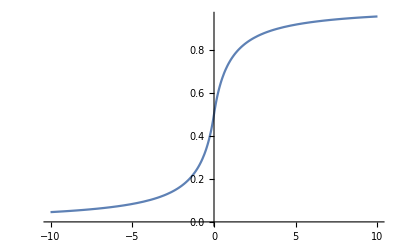

```mathematica
Plot[NarrowSoftBit[x],{x,-10,10}]
```

```mathematica
Manipulate[Plot[SoftAndIncludeNarrow[{b},{w}],{b,0,1},PlotRange->{{0,1},{0,1}},AxesLabel->Automatic],{w,0,1}]
```

```mathematica
(*Manipulate[Plot[LogSoftAndIncludeNarrow[{b},{w}],{b,0,1},PlotRange->{{0,1},{0,1}},(*PlotRange->{{0,1},{0,-20}}*)AxesLabel->Automatic],{w,0,1}]*)
```

```mathematica
Manipulate[Plot[SoftAndIncludeWide[{b},{w}],{b,-1,1},PlotRange->{{-1,1},{-1,1}},AxesLabel->Automatic],{w,-1,1}]
```

```mathematica
SoftAndIncludeWide[{b},{w}]
```

-1+2 (1-1/2 (1+1/2 (-1-b)) (1+w))

```mathematica
SoftAndIncludeWide[{b1,b2},{w1,w2}]
```

-1+2 (1-1/2 (1+1/2 (-1-b1)) (1+w1)) (1-1/2 (1+1/2 (-1-b2)) (1+w2))

```mathematica
na=NeuralAND[{1.0}]
```

NetGraph[<>]

```mathematica
Manipulate[
Block[{na=NeuralAND[{w1,w2}]},
Plot[{na[{b1,b2}],SoftAndIncludeWide[{b1,b2},{w1,w2}]},{b1,-1,1},PlotRange->{{-1,1},{-1,1}},AxesLabel->Automatic]
],
{b2,-1,1},{w1,-1,1},{w2,-1,1}
]
```

```mathematica
na=NeuralAND[{1.0,1.0}]
```

NetGraph[<>]

```mathematica
NeuralANDLayer[2,3]
```

NetGraph[<>]

## Or

```mathematica
SoftOrIncludeNarrow[b_List,w_List]:=1-Times@@MapThread[1-#1#2 &,{b,w}]
LogSoftOrIncludeNarrow[b_List,w_List]:=Log[1]-Plus@@MapThread[LogSoftBit[1-#1 #2]&,{b,w}]
SoftOrIncludeWide[b_List,w_List]:=WidenSoftBit[SoftOrIncludeNarrow[NarrowSoftBit/@b,NarrowSoftBit/@w]]
```

```mathematica
Manipulate[Plot[SoftOrIncludeNarrow[{b},{w}],{b,0,1},PlotRange->{{0,1},{0,1}},AxesLabel->Automatic],{w,0,1}]
```

```mathematica
Manipulate[Plot[LogSoftOrIncludeNarrow[{b},{w}],{b,0,1},PlotRange->{{0,1},{0,20}},AxesLabel->Automatic],{w,0,1}]
```

```mathematica
Manipulate[Plot[SoftOrIncludeWide[{b},{w}],{b,-1,1},PlotRange->{{-1,1},{-1,1}},AxesLabel->Automatic],{w,-1,1}]
```

```mathematica
SoftOrIncludeWide[{b},{w}]
```

-1+1/2 (1+b) (1+w)

```mathematica
SoftOrIncludeWide[{b1,b2},{w1,w2}]
```

-1+2 (1-(1-1/4 (1+b1) (1+w1)) (1-1/4 (1+b2) (1+w2)))

```mathematica
SoftOrIncludeWide[{b1,b2,b3},{w1,w2,w3}]
```

-1+2 (1-(1-1/4 (1+b1) (1+w1)) (1-1/4 (1+b2) (1+w2)) (1-1/4 (1+b3) (1+w3)))

```mathematica
no=NeuralOR[{1.0,1.0}]
```

NetGraph[<>]

```mathematica
Manipulate[
Block[{na=NeuralOR[{w1,w2}]},
Plot[{na[{b1,b2}],SoftOrIncludeWide[{b1,b2},{w1,w2}]},{b1,-1,1},PlotRange->{{-1,1},{-1,1}},AxesLabel->Automatic]
],
{b2,-1,1},{w1,-1,1},{w2,-1,1}
]
```

```mathematica
NeuralORLayer[2,3]
```

NetGraph[<>]

## Not

```mathematica
SoftNOTNarrow[b_List,w_List]:=1-w+b (-1+2 w)
SoftNOTWide[b_List,w_List]:=WidenSoftBit[SoftNOTNarrow[NarrowSoftBit/@b,NarrowSoftBit/@w]]
```

```mathematica
Manipulate[Plot[SoftNOTNarrow[{b},{w}],{b,0,1},PlotRange->{{0,1},{0,1}},AxesLabel->Automatic],{w,0,1}]
```

```mathematica
Manipulate[Plot[SoftNOTWide[{b},{w}],{b,-1,1},PlotRange->{{-1,1},{-1,1}},AxesLabel->Automatic],{w,-1,1}]
```

```mathematica
SoftNOTWide[{b},{w}]//Simplify
```

{b w}

```mathematica
SoftNOTWide[{b1,b2},{w1,w2}]//Simplify
```

{b1 w1,b2 w2}

```mathematica
SoftNOTWide[{b1,b2,b3},{w1,w2,w3}]//Simplify
```

{b1 w1,b2 w2,b3 w3}

```mathematica
NeuralNOTLayer[3]
```

NetGraph[<>]

```mathematica
NetFlatten[NeuralDNFLayer[2,6,3]]
```

NetGraph[<>]